```mathematica
PC4[f_,u0_,t0_, T_, h_]:= Module[{y,fi,i,k1,k2,k3,k4, t,n,ypred,j, correctorSteps=4},
n = Ceiling[(T-t0)/h];
t = Table[0+i*h,{i,0,n}];
y = Table[u0, {i,0,n}];
fi= Table[f[t0, u0], {i,0,n}];

(* Start with explicit runge kutta 4 to generate initial points *)
For[i = 1, i≤ 3,i++,
k1 = h*f[t⟦i⟧,y⟦i⟧];
k2 = h*f[t⟦i⟧+h/2,y⟦i⟧+k1/2];
k3 = h*f[t⟦i⟧+h/2,y⟦i⟧+k2/2];
k4 = h*f[t⟦i⟧+h,y⟦i⟧+k3];
y⟦i+1⟧ = y⟦i⟧ + k1/6 + k2/3 + k3/3 +k4/6;
fi[[i+1]]=f[t⟦i⟧+h,y[[i+1]]];
];


For[i=4, i<= n,i++,
(* Predictor Adams-Bashforth 4*)
ypred= y[[i]]+h/24(55*fi[[i]]-59fi[[i-1]]+37*fi[[i-2]]-9fi[[i-3]]);
(* Corrector Adams-Moulton 4*)
For[j = 1, j<= correctorSteps, j++,
ypred= y[[i]] +h/720(251f[t[[i]]+h, ypred]+646fi[[i]]-264fi[[i-1]]+106fi[[i-2]]-19fi[[i-3]]);
];

(* Save result *)
y[[i+1]]= y[[i]] +h/720(251f[t[[i]]+h, ypred]+646fi[[i]]-264fi[[i-1]]+106fi[[i-2]]-19fi[[i-3]]);
fi[[i+1]] = f[t[[i]]+h, y[[i+1]] ];
];

Return[{t,y}];
];
```

```mathematica
f[t_,u_]:= 2*u(1-u)
```

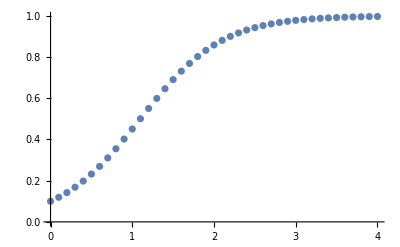

```mathematica
{t,y}=PC4[f, 0.1, 0, 4,0.1];
ListPlot[Transpose[{t,y}]]
```